```mathematica
mu = 1;
sigmat = 0.0;
sigmas =0.1;
rpsi0 = 0;
lpsi0 = 1;
X = 1;

solution = DSolve[{mu * rpsi'[x]+sigmat*rpsi[x]==1/2 sigmas * (rpsi[x]+lpsi[x]),-mu * lpsi'[x]+sigmat*lpsi[x]==1/2 sigmas*(rpsi[x]+lpsi[x]),lpsi[X]==lpsi0,rpsi[0]==rpsi0},{lpsi[x],rpsi[x]},x]
```

{{lpsi[x]→-0.0526316 ⅇ^(-1.86563×10^-19 x) (-20.+1. x),rpsi[x]→0.0526316 ⅇ^(-1.86563×10^-19 x) x}}

```mathematica
(*Used Wolfram Documentation to store to variables*)
```

```mathematica
left = lpsi[x]/.solution;
right = rpsi[x]/.solution;
```

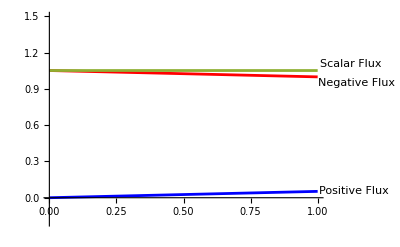

```mathematica
Plot[{Labeled[Style[left[[1]],Red],"Negative Flux"],Labeled[Style[right[[1]],Blue],"Positive Flux"],Labeled[left[[1]]+right[[1]],"Scalar Flux"]},{x,0,X},PlotRange->{{0,X},{-0.2,1.5}}]
```